# Combinatorial Resultant

Authors: Goran Malic and Ileana Streinu
Version: 1.0
Date of last change: 2022-05-26

Please contact gmalic@smith.edu for questions or comments.

## Variables

```mathematica
makeVarX[i_,j_]:=Which[
i<j,Subscript[x, i,j],
j<i,Subscript[x, j,i],
i==j,0];
```

```mathematica
makeCayleyVars[n_]:=Flatten[Table[makeVarX[i,j],{i,1,n-1},{j,i+1,n}]]
```

```mathematica
makeCayleyVarsSubsetInds[inds_]:=DeleteCases[DeleteDuplicates[Flatten[Table[makeVarX[i,j],{i,inds},{j,inds}]]],_Integer]
```

#### Unit test

```mathematica
makeCayleyVars[3]
```

{x_(1,2),x_(1,3),x_(2,3)}

```mathematica
makeCayleyVarsSubsetInds[{2,4,5}]
```

{x_(2,4),x_(2,5),x_(4,5)}

```mathematica
makeCayleyVarsSubsetInds[{2,4,6,3,5}]
```

{x_(2,4),x_(2,6),x_(2,3),x_(2,5),x_(4,6),x_(3,4),x_(4,5),x_(3,6),x_(5,6),x_(3,5)}

```mathematica
cayleyToCartesianSingleVar[Subscript[x, i_,j_]]:=Subscript[x, i,j]->(Subscript[a, i]-Subscript[a, j])^2+(Subscript[b, i]-Subscript[b, j])^2
```

```mathematica
cayleyToCartesianRule[poly_]:=cayleyToCartesianSingleVar/@Variables[poly]
```

## Cayley-Menger matrix

```mathematica
makeEuclideanPart[n_]:=Table[makeVarX[i,j],{i,1,n},{j,1,n}];
```

```mathematica
makeCayleyMengerMatrix[n_]:=Module[{euclideanPart,firstRow,otherRows},
euclideanPart=makeEuclideanPart[n];
firstRow=Prepend[ConstantArray[1,n],0];
otherRows=Table[Prepend[euclideanPart[[i]],1],{i,1,n}];
Prepend[otherRows,firstRow]
]
```

### Unit test

```mathematica
makeCayleyMengerMatrix[6]//MatrixForm
```

(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | x_(1,2) | x_(1,3) | x_(1,4) | x_(1,5) | x_(1,6)
1 | x_(1,2) | 0 | x_(2,3) | x_(2,4) | x_(2,5) | x_(2,6)
1 | x_(1,3) | x_(2,3) | 0 | x_(3,4) | x_(3,5) | x_(3,6)
1 | x_(1,4) | x_(2,4) | x_(3,4) | 0 | x_(4,5) | x_(4,6)
1 | x_(1,5) | x_(2,5) | x_(3,5) | x_(4,5) | 0 | x_(5,6)
1 | x_(1,6) | x_(2,6) | x_(3,6) | x_(4,6) | x_(5,6) | 0)

## Minors of the Cayley-Menger matrix

```mathematica
cmIdeal[n_, k_] :=DeleteDuplicates[ Flatten[Minors[makeCayleyMengerMatrix[n], k]]]
```

## Sylvester Matrix

```mathematica
(*Implementation from https://mathworld.wolfram.com/SylvesterMatrix.html*)
```

```mathematica
sylvesterMatrix[poly1_,poly2_,var_]:=Function[{coeffs1,coeffs2},With[{l1=Length[coeffs1],l2=Length[coeffs2]},Join[NestList[RotateRight,PadRight[coeffs1,l1+l2-2],l2-2],NestList[RotateRight,PadRight[coeffs2,l1+l2-2],l1-2]]]][Reverse[CoefficientList[poly1,var]],Reverse[CoefficientList[poly2,var]]]
```

## Circuit of size 4

```mathematica
(*Input: (r,s,t,u) where r<s<t<u*)
```

```mathematica
circuit4[r_,s_,t_,u_]:=Subscript[x, a,b] Subscript[x, a,c] Subscript[x, b,c]-Subscript[x, a,b] Subscript[x, a,d] Subscript[x, b,c]-Subscript[x, a,c] Subscript[x, a,d] Subscript[x, b,c]+Subscript[x, a,d]^2 Subscript[x, b,c]+Subscript[x, a,d] Subscript[x, b,c]^2-Subscript[x, a,b] Subscript[x, a,c] Subscript[x, b,d]+Subscript[x, a,c]^2 Subscript[x, b,d]+Subscript[x, a,b] Subscript[x, a,d] Subscript[x, b,d]-Subscript[x, a,c] Subscript[x, a,d] Subscript[x, b,d]-Subscript[x, a,c] Subscript[x, b,c] Subscript[x, b,d]-Subscript[x, a,d] Subscript[x, b,c] Subscript[x, b,d]+Subscript[x, a,c] Subscript[x, b,d]^2+Subscript[x, a,b]^2 Subscript[x, c,d]-Subscript[x, a,b] Subscript[x, a,c] Subscript[x, c,d]-Subscript[x, a,b] Subscript[x, a,d] Subscript[x, c,d]+Subscript[x, a,c] Subscript[x, a,d] Subscript[x, c,d]-Subscript[x, a,b] Subscript[x, b,c] Subscript[x, c,d]-Subscript[x, a,d] Subscript[x, b,c] Subscript[x, c,d]-Subscript[x, a,b] Subscript[x, b,d] Subscript[x, c,d]-Subscript[x, a,c] Subscript[x, b,d] Subscript[x, c,d]+Subscript[x, b,c] Subscript[x, b,d] Subscript[x, c,d]+Subscript[x, a,b] Subscript[x, c,d]^2/.{a->r,b->s,c->t,d->u};
```

```mathematica
(*Circuit for K4 with vertices 1234*)
circuit4[1,2,3,4]
```

x_(1,2) x_(1,3) x_(2,3)-x_(1,2) x_(1,4) x_(2,3)-x_(1,3) x_(1,4) x_(2,3)+x_(1,4)^2 x_(2,3)+x_(1,4) x_(2,3)^2-x_(1,2) x_(1,3) x_(2,4)+x_(1,3)^2 x_(2,4)+x_(1,2) x_(1,4) x_(2,4)-x_(1,3) x_(1,4) x_(2,4)-x_(1,3) x_(2,3) x_(2,4)-x_(1,4) x_(2,3) x_(2,4)+x_(1,3) x_(2,4)^2+x_(1,2)^2 x_(3,4)-x_(1,2) x_(1,3) x_(3,4)-x_(1,2) x_(1,4) x_(3,4)+x_(1,3) x_(1,4) x_(3,4)-x_(1,2) x_(2,3) x_(3,4)-x_(1,4) x_(2,3) x_(3,4)-x_(1,2) x_(2,4) x_(3,4)-x_(1,3) x_(2,4) x_(3,4)+x_(2,3) x_(2,4) x_(3,4)+x_(1,2) x_(3,4)^2

## Wheel on 4 vertices

```mathematica
(*Input: (a,b,c,d,e) where abcd is a counter-clockwise ordered cycle, and e the center vertex*)
```

```mathematica
wheel4[a_,b_,c_,d_,e_]:=Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2+4 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^4-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+4 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]]-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^4 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+4 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^4+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^4+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^4-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^4+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^4-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-16 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+6 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,d],Max[a,d]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+6 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+4 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^4 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+4 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^4 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+6 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[b,e],Max[b,e]]^4 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^4 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+4 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+6 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-5 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,d],Max[a,d]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^4 Subscript[x, Min[d,e],Max[d,e]]^2+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3-3 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,e],Max[a,e]]^3 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-3 Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[b,e],Max[b,e]]^3 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^3 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-2 Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+3 Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,d],Max[a,d]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,d],Max[c,d]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^3+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^3 Subscript[x, Min[d,e],Max[d,e]]^3-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^4+Subscript[x, Min[a,e],Max[a,e]]^2 Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^4+Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[d,e],Max[d,e]]^4+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^4-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^4+Subscript[x, Min[a,b],Max[a,b]]^2 Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^4-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^4-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^4-Subscript[x, Min[a,e],Max[a,e]] Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^4-Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^4+Subscript[x, Min[b,c],Max[b,c]] Subscript[x, Min[b,e],Max[b,e]]^2 Subscript[x, Min[c,e],Max[c,e]] Subscript[x, Min[d,e],Max[d,e]]^4+Subscript[x, Min[a,b],Max[a,b]] Subscript[x, Min[b,e],Max[b,e]] Subscript[x, Min[c,e],Max[c,e]]^2 Subscript[x, Min[d,e],Max[d,e]]^4
```

## Support To Graph

```mathematica
supportToGraph[support_]:=Module[
{edges,i},
edges=Table[support[[i,2]]->support[[i,3]],{i,1,Length[support]}];
GraphComputation`GraphPlotLegacy[edges,VertexLabeling->True]
]
```

### Test

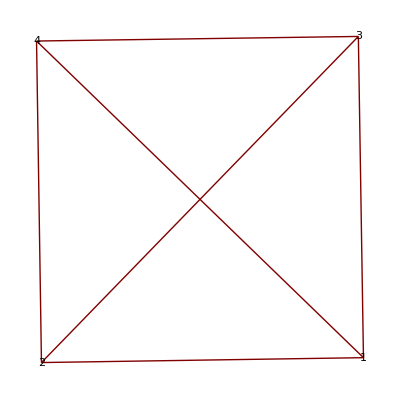

```mathematica
supportToGraph[Variables[circuit4[1,2,3,4]]]
```

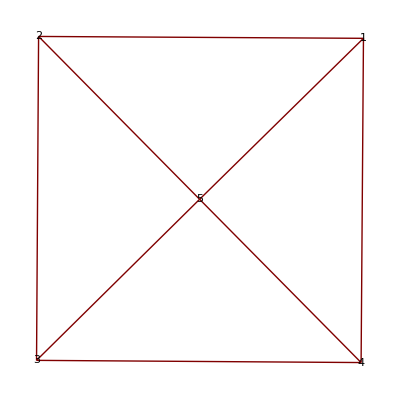

```mathematica
supportToGraph[Variables[wheel4[1,2,3,4,5]]]
```

## Vertex Relabeling

```mathematica
(*
  First argument is the polynomial whose support we want to relabel

Second argument is a list {a->b,c->d,e->f,...} of replacement rules
where a->b indicates that the vertex a is to be relabelled into the vertex b
*)
vertexSub[poly_,list_]:=Module[{support,indexList={},newIndices,newVars,subRule={}},
support=Variables[poly];
Do[AppendTo[indexList,{support[[i]][[2]],support[[i]][[3]]}],{i,1,Length[support]}];newIndices=indexList/.list;
newVars=makeVarX@@@newIndices;
Do[
If[support[[j]]=!=newVars[[j]],
AppendTo[subRule,support[[j]]->newVars[[j]]]
],{j,1,Length[support]}];
poly/.subRule
]
```

### Test

```mathematica
vertexSub[circuit4[1,2,3,4],{1->2,2->3,3->4,4->5}]-circuit4[2,3,4,5]
```

0

## Tutorial: computing the Desargues-plus-one circuit

```mathematica
(*We recommend to use a machine with at least 8GB of RAM. We have not tested the code below on a machine with less RAM.*)
```

We initialize first the circuit polynomial for W4 on 1234 with 5 in the center, and a K4 on the vertices 2356.

```mathematica
pW4=wheel4[1,2,3,4,5];
pK4=circuit4[2,3,5,6];
```

Now we compute the resultant of pW4 and pK4 w.r.t. x35

```mathematica
r=Resultant[pW4,pK4,Subscript[x, 3,5]];
```

We can visualise the support of r as follows

```mathematica
supportToGraph[Variables[r]]
```

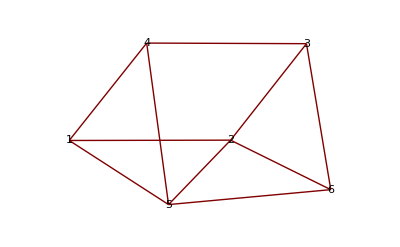

The support of r indeed corresponds to a Desargues-plus-one graph. To conclude that it is the circuit polynomial for it, we have to verify irreducibility.

```mathematica
IrreduciblePolynomialQ[r]
```

True